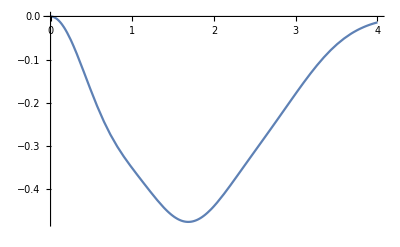

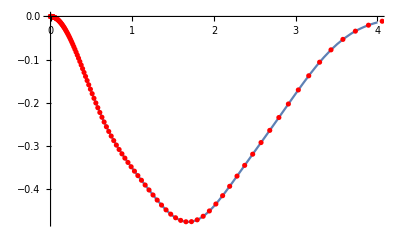

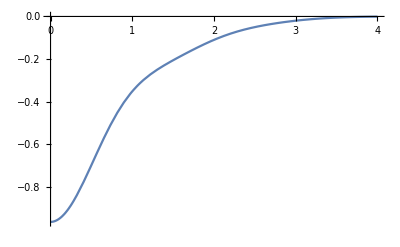

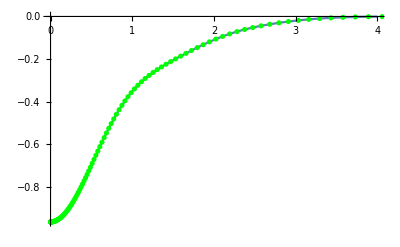

-0.999998

```mathematica
Clear["Global`*"];
data=ReadList["C:\\Users\\yw3c\\Desktop\\sValue.txt"];
(*Print[MatrixForm[data]];*)
NumOfPoints=Length[data]/2;
For[i=1,i<NumOfPoints+1,i++,
s[i]=data[[2*i]];
sxhole[i]=data[[2*i-1]];
];
s[1];
IntData=Table[{s[i],s[i]^2*sxhole[i]},{i,NumOfPoints}];
OriData=Table[{s[i],sxhole[i]},{i,NumOfPoints}];
f=Interpolation[IntData];
f2=Interpolation[OriData];
Plot[f[x],{x,s[1],4}]
Show[%,ListPlot[IntData,PlotStyle->{Red}]]
Plot[f2[x],{x,s[1],4}]
Show[%,ListPlot[OriData,PlotStyle->{Green}]]
N[NIntegrate[f[x],{x,0,Infinity}],18]
```